```mathematica
<<MaTeX`
texStyle={FontFamily->"Latin Modern Math",FontSize->20};
SetOptions[MaTeX,"Preamble"->{"\\usepackage{color}"}];
SetDirectory[NotebookDirectory[]];
```

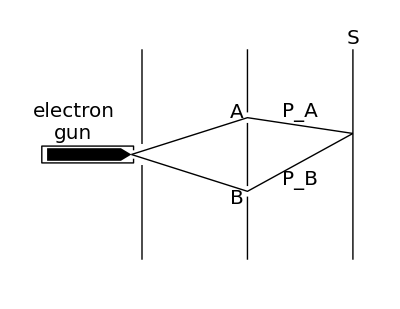

./Figure/Fig2-1.pdf

```mathematica
Subscript[fig2, 1]=Graphics[{Line[{{0,1},{0,0.1}}],Line[{{0,-1},{0,-0.1}}],Line[{{1,-1},{1,-0.4}}],Line[{{1,0.3},{1,-0.3}}],Line[{{1,0.4},{1,1}}],Line[{{2,-1},{2,1}}],Line[{{-0.1,0},{1,0.35},{2,0.2}}],Line[{{-0.1,0},{1,-0.35},{2,0.2}}],Polygon[{{-0.2,0.06},{-0.9,0.06},{-0.9,-0.06},{-0.2,-0.06},{-0.1,0}}],Line[{{-0.08,0.04},{-0.08,0.08},{-0.95,0.08},{-0.95,-0.08},{-0.08,-0.08},{-0.08,-0.04}}]},Epilog->{Inset[Style["A",texStyle],{0.9,0.4}],Inset[Style["B",texStyle],{0.9,-0.42}],Inset[Style["S",texStyle],{2,1.1}],Inset[Style["P_A",texStyle],{1.5,0.4}],Inset[Style["P_B",texStyle],{1.5,-0.25}],Inset[Style["electron
gun",texStyle,TextAlignment->Left],{-0.65,0.3}]},PlotRange->{{-1,2.1},{-1.2,1.2}},ImageSize->400]
Export["./Figure/Fig2-1.pdf",Subscript[fig2, 1]]
```

```mathematica
arr[lst_]:=Table[{Arrow[{lst[[i]],(lst[[i]]+lst[[i+1]])/2}],Line[{(lst[[i]]+lst[[i+1]])/2,lst[[i+1]]}]},{i,Length[lst]-1}]
```

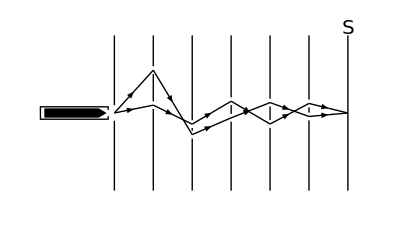

./Figure/Fig2-2a.pdf

```mathematica
Subscript[fig2, 2a]=Graphics[{Line[{{0,1},{0,0.1}}],Line[{{0,-1},{0,-0.1}}],Line[{{3,1},{3,-1}}],Table[{Line[{{j/2,1},{j/2,Max[Sin[2j]Exp[-j/2],Sin[3j]Exp[-j/3]]+0.05}}],Line[{{j/2,Min[Sin[2j]Exp[-j/2],Sin[3j]Exp[-j/3]]+0.05},{j/2,Max[Sin[2j]Exp[-j/2],Sin[3j]Exp[-j/3]]-0.05}}],Line[{{j/2,-1},{j/2,Min[Sin[2j]Exp[-j/2],Sin[3j]Exp[-j/3]]-0.05}}]},{j,5}],arr[Join[Table[{j/2,Sin[2j]Exp[-j/2]},{j,0,5}],{{3,0}}]],arr[Join[Table[{j/2,Sin[3j]Exp[-j/3]},{j,0,5}],{{3,0}}]],Polygon[{{-0.2,0.06},{-0.9,0.06},{-0.9,-0.06},{-0.2,-0.06},{-0.1,0}}],Line[{{-0.08,0.04},{-0.08,0.08},{-0.95,0.08},{-0.95,-0.08},{-0.08,-0.08},{-0.08,-0.04}}]},Epilog->{Inset[Style["S",texStyle],{3,1.1}]},PlotRange->{{-1,3.2},{-1.2,1.2}},ImageSize->400]
Export["./Figure/Fig2-2a.pdf",Subscript[fig2, 2a]]
```

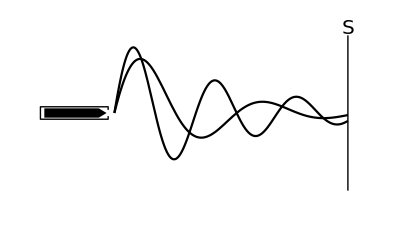

./Figure/Fig2-2b.pdf

```mathematica
Subscript[fig2, 2b]=Show[Graphics[{Line[{{3,1},{3,-1}}],Polygon[{{-0.2,0.06},{-0.9,0.06},{-0.9,-0.06},{-0.2,-0.06},{-0.1,0}}],Line[{{-0.08,0.04},{-0.08,0.08},{-0.95,0.08},{-0.95,-0.08},{-0.08,-0.08},{-0.08,-0.04}}]},Epilog->{Inset[Style["S",texStyle],{3,1.1}]},PlotRange->{{-1,3.2},{-1.2,1.2}},ImageSize->400],Plot[{Sin[6x]Exp[-x/1.5],Sin[4x]Exp[-x]},{x,0,3},PlotRange->All,PlotStyle->{Black,Black}]]
Export["./Figure/Fig2-2b.pdf",Subscript[fig2, 2b]]
```